# QCD calculation: 1-Loop Calculation

### Initialization

```mathematica
Quit[];
```

```mathematica
$Language="English";
<<FeynArts`
<<FormCalc`

(* helicity averaged *)
_Hel=0;
```

FeynArts 3.9 (23 Sep 2015)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.4 (7 Jun 2016)

by Thomas Hahn

### Create Topology

> Top. 1: 1 diagram

> Top. 2: 1 diagram

> Top. 3: 1 diagram

> Top. 4: 1 diagram

> Top. 5: 1 diagram

> Top. 6: 1 diagram

> Top. 7: 1 diagram

> Top. 8: 1 diagram

> Top. 9: 1 diagram

> Top. 10: 1 diagram

> Top. 11: 1 diagram

> Top. 12: 1 diagram

> Top. 13: 1 diagram

> Top. 14: 1 diagram

> Top. 15: 1 diagram

> Top. 16: 1 diagram

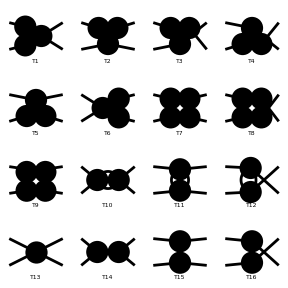

```mathematica
topo0=CreateTopologies[0,2->2];
topo1=CreateTopologies[1,2->2,ExcludeTopologies->{Internal}];
topologies=Join[topo1,topo0];
Paint[topologies, ColumnsXRows->4];
```

### u ū → c c̄ : tree-level diagrams and tree + 1-loop diagrams

loading generic model file /Users/misho/HEPcodes/FeynArts/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/misho/HEPcodes/FeynArts/Models/SMQCD.mod

loading classes model file /Users/misho/HEPcodes/FeynArts/Models/SM.mod

$CKM=False

> 49 particles (incl. antiparticles) in 18 classes

> $CounterTerms are ON

> 93 vertices

> 121 counter terms of order 1

> 6 counter terms of order 2

classes model {SMQCD} initialized

Excluding 0 Generic, 8 Classes, and 8 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

Restoring 0 Generic, 8 Classes, and 8 Particles fields

in total: 1 Classes insertion

Excluding 0 Generic, 8 Classes, and 8 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

> Top. 5: 0 Classes insertions

> Top. 6: 0 Classes insertions

> Top. 7: 1 Classes insertion

> Top. 8: 1 Classes insertion

> Top. 9: 0 Classes insertions

> Top. 10: 0 Classes insertions

> Top. 11: 0 Classes insertions

> Top. 12: 0 Classes insertions

Restoring 0 Generic, 8 Classes, and 8 Particles fields

in total: 2 Classes insertions

> Top. 1: 1 diagram

> Top. 2: 1 diagram

> Top. 3: 1 diagram

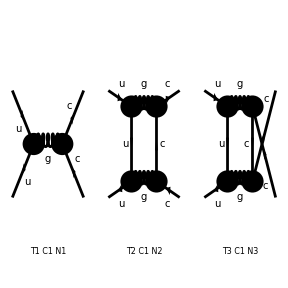

```mathematica
process={F[3,{1}],-F[3,{1}]}->{F[3,{2}],-F[3,{2}]};
TreeDiagrams = InsertFields[topo0,process,InsertionLevel->{Classes},Model->"SMQCD",
ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2],S[3]}];
OneLoopDiagrams = InsertFields[topo1,process,InsertionLevel->{Classes},Model->"SMQCD",
ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2],S[3]}];
Paint[Join[TreeDiagrams,OneLoopDiagrams]];
```

### Tree-level amplitude

```mathematica
ClearProcess[];
TreeMatrixSquared=Module[{amp,mat},
amp = CalcFeynAmp[CreateFeynAmp[TreeDiagrams],FermionChains->VA];
mat = 4/9 SquaredME[amp] //. HelicityME[amp] //. ColourME[amp];
FullSimplify[mat /. Den[a_, b_] :> 1/(a-b),S+T+U==2MU2+2MC2]]
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

preparing FORM code in /Users/misho/fc-amp-2.frm

running FORM...

ok

> 1 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-2.frm

running FORM...

ok

(32 Alfas2 π^2 (3 S^2+(T-U)^2+2 S (T+U)))/(9 S^2)

Now the variable “TreeMatrixSquared” has no abbreviations / subexpressions.
So ClearProcess[] without losing any information, and we can evaluate the next diagram.

### Tree + 1-loop level amplitude

```mathematica
ClearProcess[];
OneLoopAmp = CalcFeynAmp[CreateFeynAmp[Join[TreeDiagrams,OneLoopDiagrams]],FermionChains->VA]
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

in total: 3 Classes amplitudes

preparing FORM code in /Users/misho/fc-amp-2.frm

running FORM...

ok

Amp[{{F[3,{1,Col1}],k[1],MU,{(2 Charge)/3,(2 ColorCharge)/(√3)}},{-F[3,{1,Col2}],k[2],MU,{-(2 Charge)/3,-(2 ColorCharge)/(√3)}}}→{{F[3,{2,Col3}],k[3],MC,{(2 Charge)/3,(2 ColorCharge)/(√3)}},{-F[3,{2,Col4}],k[4],MC,{-(2 Charge)/3,-(2 ColorCharge)/(√3)}}}][(-Alfas2 (7/3 C0i[cc0,S,MC2,MC2,0,0,MC2]-7/2 D0i[dd00,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+5/3 D0i[dd00,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+(MC2+MU2-U) (1/3 D0i[dd0,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]-7/3 (D0i[dd1,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd11,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2])+2/3 (D0i[dd1,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd11,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]))-7/3 (2 MC2+MU2-U) D0i[dd12,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+(MU2-U) (2/3 D0i[dd12,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+1/3 D0i[dd2,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2])+MC2 (-7/2 D0i[dd22,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+1/3 D0i[dd22,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2])-7/24 (11 (MC2+MU2)-3 T) D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-1/12 Sub1 D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]-7/6 ((MC2+MU2-S-U) D0i[dd0,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+(2 MC2+MU2-T) D0i[dd2,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+Sub2 D0i[dd3,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2])+(MC2+2 MU2-U) (-7/3 D0i[dd13,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+2/3 D0i[dd13,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+1/3 D0i[dd3,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2])+MU2 (-7/2 D0i[dd33,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd33,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]))-2 Alfas π Den[S,0]) Mat[F1 SUN1]-Alfas2 MC (7/2 D0i[dd22,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+1/3 D0i[dd22,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+7/3 (D0i[dd12,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd2,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2])+2/3 (D0i[dd12,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd2,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2])) Mat[F10 SUN1]-Alfas2 MC (2/3 D0i[dd12,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+7/3 (D0i[dd12,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd22,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2])+7/6 (D0i[dd2,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2])+1/3 (D0i[dd2,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2])) Mat[F11 SUN1]-Alfas2 MC (7/6 D0i[dd22,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-1/3 D0i[dd22,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]) Mat[F12 SUN1]-Alfas2 MC (2/3 D0i[dd12,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+7/3 (D0i[dd12,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd22,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2])+7/6 (D0i[dd2,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2])+1/3 (D0i[dd2,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2])) Mat[F13 SUN1]+Alfas2 (14/3 (D0i[dd1,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd11,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd12,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd13,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2])-4/3 (D0i[dd1,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd11,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd12,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd13,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2])-7/6 D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]) Mat[F14 SUN1]-Alfas2 (7/12 D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+1/6 D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]) Mat[F15 SUN1]+Alfas2 (7/24 D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+1/12 D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]) Mat[F16 SUN1]+Alfas2 (7/12 D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+1/6 D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]) Mat[F17 SUN1]-Alfas2 (7/24 D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+1/12 D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]) Mat[F18 SUN1]+Alfas2 (7/12 D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+1/6 D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]) Mat[F19 SUN1]+Alfas2 MU (7/6 D0i[dd3,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-1/3 D0i[dd3,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+7/3 (D0i[dd13,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd33,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2])-2/3 (D0i[dd13,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd33,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2])) Mat[F2 SUN1]+Alfas2 (7/12 D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+1/6 D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]) Mat[F20 SUN1]-Alfas2 (7/12 D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+1/6 D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]) Mat[F21 SUN1]-Alfas2 MC (7/6 D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+1/3 D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]) Mat[F22 SUN1]-Alfas2 MC (7/6 D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+1/3 D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]) Mat[F23 SUN1]-Alfas2 (7/12 D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+1/6 D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]) Mat[F24 SUN1]+Alfas2 (7/6 D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+1/3 D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]) Mat[F25 SUN1]+Alfas2 MC MU (7/24 D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+1/12 D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]) Mat[F3 SUN1]+Alfas2 MC MU (7/24 D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+1/12 D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]) Mat[F4 SUN1]-Alfas2 MU (2/3 D0i[dd13,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]-7/3 (D0i[dd13,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd3,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2])-7/2 D0i[dd33,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+1/3 D0i[dd33,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]) Mat[F5 SUN1]+Alfas2 MU (7/6 D0i[dd3,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-1/3 D0i[dd3,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+7/3 (D0i[dd13,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd33,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2])-2/3 (D0i[dd13,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd33,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2])) Mat[F6 SUN1]-Alfas2 MC MU (2/3 (D0i[dd12,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2])+7/3 (D0i[dd12,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd13,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd2,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd22,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd3,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd33,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2])-2/3 (D0i[dd13,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd3,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd33,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2])) Mat[F7 SUN1]+Alfas2 MU (7/6 D0i[dd33,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-1/3 D0i[dd33,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]) Mat[F8 SUN1]-Alfas2 (7/2 D0i[dd00,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-D0i[dd00,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+MC2 (7/6 D0i[dd22,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-1/3 D0i[dd22,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2])+(MC2+MU2-T) (7/8 D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+1/4 D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2])+MU2 (7/6 D0i[dd33,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-1/3 D0i[dd33,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2])) Mat[F9 SUN1]+(-Alfas2 (1/9 C0i[cc0,S,MC2,MC2,0,0,MC2]-1/6 D0i[dd00,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-25/9 D0i[dd00,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+(MC2+MU2-U) (-5/9 D0i[dd0,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+1/9 (-D0i[dd1,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-D0i[dd11,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2])-10/9 (D0i[dd1,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd11,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]))-1/9 (2 MC2+MU2-U) D0i[dd12,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+1/18 (-(MC2+MU2-S-U) D0i[dd0,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-(2 MC2+MU2-T) D0i[dd2,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2])+(MU2-U) (-10/9 D0i[dd12,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]-5/9 D0i[dd2,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2])+MC2 (-1/6 D0i[dd22,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-5/9 D0i[dd22,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2])-1/72 (11 (MC2+MU2)-3 T) D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+5/36 Sub1 D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]-1/18 Sub2 D0i[dd3,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+(MC2+2 MU2-U) (-1/9 D0i[dd13,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-10/9 D0i[dd13,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]-5/9 D0i[dd3,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2])+MU2 (-1/6 D0i[dd33,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-5/3 D0i[dd33,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]))+2/3 Alfas π Den[S,0]) Mat[F1 SUN2]-Alfas2 MC (1/6 D0i[dd22,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-5/9 D0i[dd22,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+1/9 (D0i[dd12,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd2,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2])-10/9 (D0i[dd12,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd2,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2])) Mat[F10 SUN2]+Alfas2 MC (10/9 D0i[dd12,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+1/9 (-D0i[dd12,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-D0i[dd22,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2])+1/18 (-D0i[dd2,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2])+5/9 (D0i[dd2,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2])) Mat[F11 SUN2]-Alfas2 MC (1/18 D0i[dd22,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+5/9 D0i[dd22,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]) Mat[F12 SUN2]+Alfas2 MC (10/9 D0i[dd12,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+1/9 (-D0i[dd12,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-D0i[dd22,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2])+1/18 (-D0i[dd2,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2])+5/9 (D0i[dd2,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2])) Mat[F13 SUN2]+Alfas2 (2/9 (D0i[dd1,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd11,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd12,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd13,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2])+20/9 (D0i[dd1,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd11,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd12,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd13,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2])-1/18 D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+5/3 D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]) Mat[F14 SUN2]-Alfas2 (1/36 D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-5/18 D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]) Mat[F15 SUN2]+Alfas2 (1/72 D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-5/36 D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]) Mat[F16 SUN2]+Alfas2 (1/36 D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-5/18 D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]) Mat[F17 SUN2]-Alfas2 (1/72 D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-5/36 D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]) Mat[F18 SUN2]+Alfas2 (1/36 D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-5/18 D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]) Mat[F19 SUN2]+Alfas2 MU (1/18 D0i[dd3,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+5/9 D0i[dd3,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+1/9 (D0i[dd13,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd33,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2])+10/9 (D0i[dd13,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd33,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2])) Mat[F2 SUN2]+Alfas2 (1/36 D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-5/18 D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]) Mat[F20 SUN2]-Alfas2 (1/36 D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-5/18 D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]) Mat[F21 SUN2]-Alfas2 MC (1/18 D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-5/9 D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]) Mat[F22 SUN2]-Alfas2 MC (1/18 D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-5/9 D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]) Mat[F23 SUN2]-Alfas2 (1/36 D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-5/18 D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]) Mat[F24 SUN2]+Alfas2 (1/18 D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-5/9 D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]) Mat[F25 SUN2]+Alfas2 MC MU (1/72 D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-5/36 D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]) Mat[F3 SUN2]+Alfas2 MC MU (1/72 D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-5/36 D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]) Mat[F4 SUN2]+Alfas2 MU (10/9 D0i[dd13,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+1/9 (D0i[dd13,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd3,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2])+1/6 D0i[dd33,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+5/9 D0i[dd33,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]) Mat[F5 SUN2]+Alfas2 MU (1/18 D0i[dd3,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+5/9 D0i[dd3,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+1/9 (D0i[dd13,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd33,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2])+10/9 (D0i[dd13,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd33,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2])) Mat[F6 SUN2]+Alfas2 MC MU (10/9 (D0i[dd12,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2])+1/9 (-D0i[dd12,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-D0i[dd13,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-D0i[dd2,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-D0i[dd22,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-D0i[dd3,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-D0i[dd33,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2])-10/9 (D0i[dd13,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd3,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+D0i[dd33,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2])) Mat[F7 SUN2]+Alfas2 MU (1/18 D0i[dd33,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+5/9 D0i[dd33,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]) Mat[F8 SUN2]-Alfas2 (1/6 D0i[dd00,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+5/3 D0i[dd00,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2]+MC2 (1/18 D0i[dd22,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+5/9 D0i[dd22,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2])+(MC2+MU2-T) (1/24 D0i[dd23,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]-5/12 D0i[dd23,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2])+MU2 (1/18 D0i[dd33,S,MC2,T,MU2,MC2,MU2,0,0,MC2,MU2]+5/9 D0i[dd33,S,MC2,U,MU2,MC2,MU2,0,0,MC2,MU2])) Mat[F9 SUN2]]

```mathematica
OneLoopMatrixSquared=4/9 SquaredME[OneLoopAmp]//.HelicityME[OneLoopAmp]//.ColourME[OneLoopAmp]
```

> 625 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-2.frm

running FORM...

ok

4/9 (1)
 |  |  |  |

### Numerical Evaluation with LoopTools

You can load LoopTools by:

```mathematica
Install["LoopTools"]
```

s::shdw: Symbol \!\(\*RowBox[{"\"s\""}]\) appears in multiple contexts \!\(\*RowBox[{"{", RowBox[{"\"LoopTools`\"", ",", "\"FormCalc`\""}], "}"}]\); definitions in context \!\(\*RowBox[{"\"LoopTools`\""}]\) may shadow or be shadowed by other definitions.

LinkObject[…]

Now we can evaluate the Passarino-Veltman integrals with LoopTools.
For example,

```mathematica
D0i[dd1,5,1,-2,1,1,1,1,1,1,1]
```

-0.0331433-0.235571 ⅈ

So,

```mathematica
rules = Join[Subexpr[],
{Den[a_,b_]:>1/(a-b)},
{S->(2EE)^2,T->-(2 EE^2-MU2-MC2)+2 √(EE^2-MU2)√(EE^2-MC2)Cosθ,U->2MC2+2MU2-S-T}];
TreeForEvaluation = TreeMatrixSquared//.rules;
OneLoopForEvaluation = OneLoopMatrixSquared //. rules;
```

```mathematica
parameters={EE->500,MU->0.001,MU2->0.001^2,MC->173,MC2->173^2,Alfas->gs^2/(4π),Alfas2->(gs^2/(4π))^2};
{TreeForEvaluation,OneLoopForEvaluation}/.parameters/.Cosθ->0.5//FullSimplify
```

ffxc0i: infra-red divergent threepoint function, working with a cutoff    1.0000000000000000     
 ffxdbd: using IR cutoff lambda^2 =    1.0000000000000000

{0.29773 gs^4,0.29773 gs^4-0.125654 gs^6+0.0208943 gs^8}

Note that the IR-divergence is detected.
You should be aware of the IR/UV divergences BEFORE you write computation code!

We can verify the presence of IR divergence by changing λ^2 (fictious gluon mass).
The result does depend on λ^2, so IR divergence is not cancelled.

```mathematica
SetLambda[1];
Chop[FullSimplify[OneLoopForEvaluation/.parameters/.Cosθ->0.5]]
SetLambda[0.1^2];
Chop[FullSimplify[OneLoopForEvaluation/.parameters/.Cosθ->0.5]]
SetLambda[10^2];
Chop[FullSimplify[OneLoopForEvaluation/.parameters/.Cosθ->0.5]]
```

0.29773 gs^4-0.125654 gs^6+0.0208943 gs^8

0.29773 gs^4-1.63328 gs^6+2.25363 gs^8

0.29773 gs^4+1.38197 gs^6+1.60712 gs^8

In dimensional regularization, it will be

```mathematica
SetLambda[-2];
pole2=OneLoopForEvaluation/.parameters/.Cosθ->0.5;
SetLambda[-1];
pole1=OneLoopForEvaluation/.parameters/.Cosθ->0.5;
SetLambda[0];
finite=OneLoopForEvaluation/.parameters/.Cosθ->0.5;
Collect[Chop[Expand[pole2/ϵ^2+pole1/ϵ+finite]],gs]
```

gs^8 (0.0208943+0.0900376/ϵ)+gs^4 (0.29773+0.29773/ϵ^2+0.29773/ϵ)+gs^6 (-0.125654+0.327377/ϵ)